9

{{100,0,0,0,0,0,0,0,0,0,0,0},{31,69,0,0,0,0,0,0,0,0,0,0},{19,36,45,0,0,0,0,0,0,0,0,0},{16,15,30,39,0,0,0,0,0,0,0,0},{13,8,26,20,33,0,0,0,0,0,0,0},{11,8,12,24,18,28,0,0,0,0,0,0},{9,9,5,20,16,19,23,0,0,0,0,0},{8,9,4,11,19,11,21,19,0,0,0,0},{7,8,4,5,15,15,9,21,15,0,0,0},{6,7,5,3,10,16,10,9,20,13,0,0},{5,6,5,2,6,13,14,7,11,19,11,0},{5,6,6,3,3,9,13,10,6,12,18,10}}

{100,100,100,100,100,101,101,102,99,99,99,101}

0.025448 (2+Cos[t]-Sin[t]+t Sin[t]^2+Sin[t]^9)

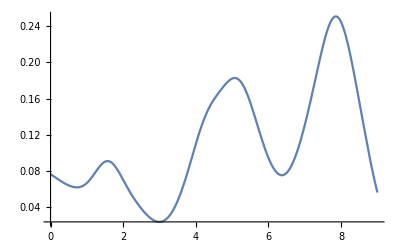

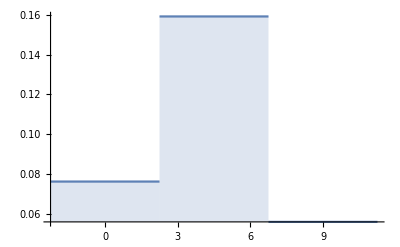

```mathematica
T=RandomInteger[{1,20}]
stake =100;
blocks = 3;
f[x_] = (x*Sin[x]^2+D[Cos[x],{x,T}]+D[Sin[x],{x,T}]+Sin[x]^T+2);
F[x_] = f[t]/NIntegrate[f[t],{t,0,T}];
S = Table[Table[Round[stake*NIntegrate[F[t],{t,i*T/rounds,(i+1)*T/rounds}]],{i,0,rounds-1}],{rounds,1,12,1}];
padS = Table[PadRight[Part[S,i],12],{i,1,12}]
check=Table[Sum[Part[padS,i,j],{j,1,Length[Part[S,i]]}],{i,1,12}]
F[x]
Plot[F[t],{t,0,T},PlotRange->Full ]
DiscretePlot[F[t],{t,0,T, T/(blocks-1)},ExtentSize->Full,ExtentMarkers->None]
```